## Homework assignment

The reaction - diffusion equations that describe the formation of a morphogen gradient are partial differential equations, i.e. they have derivatives with respect to time and derivatives with respect to space in the same equations.

Mathematica can numerically solve most partial differential equations.  The syntax is very similar to the way we used NDSolve to solve ordinary differential equations:

#### Example 1 : we use NDSolve for this ordinary differential equation system :

```mathematica
example1={y'[t] == a y[t]/(1+ b*y[t])- k y[t]^2, y[0]==10}
```

{y'[t]==-k y[t]^2+(a y[t])/(1+b y[t]),y[0]==10}

```mathematica
solset1=Block[{a=2, b=1 , k=0.1},Flatten[NDSolve[example1, y[t], {t, 0, 100}]]]
```

{y[t]→InterpolatingFunction[…][t]}

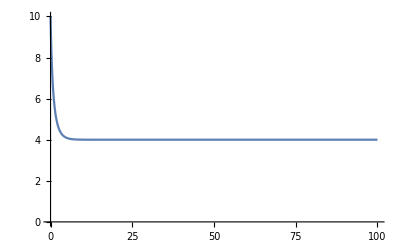

```mathematica
Plot[y[t]/.solset1, {t, 0, 100}, PlotRange-> {0, 10}]
```

#### Example 2 : we use NDSolve for this partial differential equation system (which has both space and time derivatives)

```mathematica
example2={D[y[x,t], t] ==d D[y[x,t],{x,2}]+ a y[x,t]/(1+ b*y[x,t])- k y[x,t]^2, y[x,0]==10(1-x/2)^5, y[0,t]==10, y[2,t]== 0}
```

{y^(0,1)[x,t]==-k y[x,t]^2+(a y[x,t])/(1+b y[x,t])+d y^(2,0)[x,t],y[x,0]==10 (1-x/2)^5,y[0,t]==10,y[2,t]==0}

Notice that in addition to the equation, we need one initial condition y[x,0]== (i.e. at time zero the value of y is specified for all x), and two boundary conditions y[0,t] == and y[2,t]== (i.e. at x-positions 0 and 2, the value of y is specified for all time.

```mathematica
solset2=Block[{a=2, k=0.001, b=4, d=0.1},Flatten[NDSolve[example2, y[x,t],{x,0,2}, {t, 0, 10}]]]
```

{y[x,t]→InterpolatingFunction[…][x,t]}

Note the syntax of NDSolve now has not just “{t,0,10}” but also “{x, 0, 2}”, where 0 and 2 are the boundaries on x  (they don’t have to be 0 and 2; they can be whatever numbers you choose, but make sure those are the same ones you use in your boundary conditions.

```mathematica
Plot3D[y[x,t]/.solset2, {x, 0, 2}, {t, 0, 10}, AxesLabel-> {"x","t","y"}]
```

-Graphics3D-

Instead of plotting in two dimensions, we have both time and space variables so it is natural to plot in three dimensions.  Of course sometimes you only want to see a slice through this surface.  For example, suppose you want to see the shape of the spatial curve at a fixed point in time, e.g. t=1:

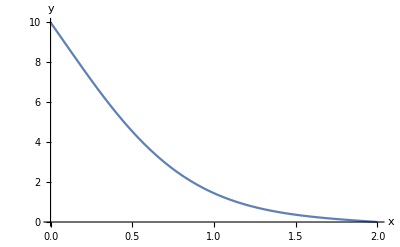

```mathematica
Plot[y[x,t]/.solset2/.t-> 1, {x, 0, 2}, AxesLabel-> {"x","y"}]
```

Or suppose you want to see how the value changes with time at a fixed location, say x=1.1

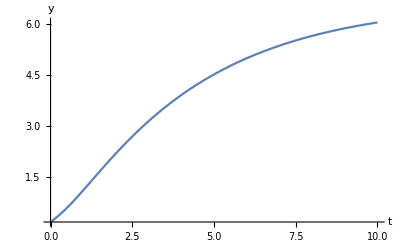

```mathematica
Plot[y[x,t]/.solset2/.x->1.1, {t, 0, 10}, AxesLabel-> {"t","y"}, PlotRange-> All]
```

#### Homework assignment:

Consider the morphogen gradient equation:

```mathematica
Derivative[0,1][y][x,t]==d Derivative[2,0][y][x,t]-k y[x,t]
```

1. Use NDSolve to solve this equation, for some value of parameters d and k of your choosing, for some amount of time t=tfinal, starting from initial conditions of y=0 everywhere, and for  boundary conditions y=1 at x=0 and y=0 at x=xmax.  In other words, you have four parameters to specify:  d, k, tfinal and xmax.  

(Note, when you solve this, if NDSolve gives you a warning message that the initial and boundary conditions are inconsistent, don’t worry about it; it’s just pointing out that at t= 0 and x=0, your initial conditions state that y=0 but your boundary conditions state that y=1.  This inconsistency only lasts for one time step and ends up not causing a significant error in the results)

Plot the result in 3D, and if necessary adjust your choice of tfinal so that you are confident the solution has reached close to steady state by t=tfinal (i.e. the curve looks like it is not changing much in time).  

2. Next, plot the result in 2D, as a function of time, at a value of x that is half-way from one boundary to the other (i.e. x=xmax/2).  Determine the time it takes for the value of the morphogen at this location to reach 1/2 of its final (steady state) value.  If you wish, you may use the analytical formula that we derived in class for determining the exact value of the steady state.  

3. How does the time it takes for the value of the morphogen to reach half-way to steady state compare with the average time it takes a molecule diffusing in free solution to travel the same distance? (the formula for this is t = x^2/(2d), where x is distance and d is the diffusion coefficient).  Are these two times similar or very different?  Why do you think that is?

4. Find the general solution of the equation on the domain 0<x<1 with Flux boundary conditions:

y^(1,0)(0,t)=y^(1,0)(1,t)=0

5. Find the general solution of the equation on the domain 0<x<1 with Flux boundary conditions:

```mathematica
Derivative[1,0][y](0,t)=1, Derivative[1,0][y](1,t)=0
```